Solving the Freund system of n^2 equations for force

## Manually defining the system

First we need to define the relevant functions (technically “patterns”)
Then we'll define our system constants
Finally, we’ll semi-manually define the system of equations and solve it. We’re interested in the force exerted at a given distance so we’ll use a constant c and solve for each mode’s f

{{f11→(8 √(5/3) ⅇ^(-80/3 c^2 π^4) π^(3/2))/Erf[4 √(5/3) c π^2],f12→(20 √(5/3) ⅇ^(-500/3 c^2 π^4) π^(3/2))/Erf[10 √(5/3) c π^2],f13→(40 √(5/3) ⅇ^(-2000/3 c^2 π^4) π^(3/2))/Erf[20 √(5/3) c π^2],f21→(20 √(5/3) ⅇ^(-500/3 c^2 π^4) π^(3/2))/Erf[10 √(5/3) c π^2],f22→(32 √(5/3) ⅇ^(-1280/3 c^2 π^4) π^(3/2))/Erf[16 √(5/3) c π^2],f23→(52 √(5/3) ⅇ^(-3380/3 c^2 π^4) π^(3/2))/Erf[26 √(5/3) c π^2],f31→(40 √(5/3) ⅇ^(-2000/3 c^2 π^4) π^(3/2))/Erf[20 √(5/3) c π^2],f32→(52 √(5/3) ⅇ^(-3380/3 c^2 π^4) π^(3/2))/Erf[26 √(5/3) c π^2],f33→(24 √15 ⅇ^(-2160 c^2 π^4) π^(3/2))/Erf[12 √15 c π^2]}}

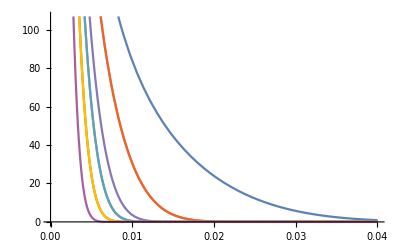

```mathematica
sigma[n_,k_,p_,q_] := n/(2*(Pi^2)*Sqrt[k]*(p^2+q^2));
f[s_,c_,f_] := Sqrt[2/Pi]*Exp[-c^2/(2*s^2)]/(s*Erf[c/(Sqrt[2]*s)])==f;

n = 3;
kappa = 30;

(*Let's solve for the force from each mode at a constant confinement distance, c*)
sys = {f[sigma[n,kappa,1,1],c,f11], f[sigma[n,kappa,1,2],c,f12], f[sigma[n,kappa,1,3],c,f13],
f[sigma[n,kappa,2,1],c,f21], f[sigma[n,kappa,2,2],c,f22], f[sigma[n,kappa,2,3],c,f23],
f[sigma[n,kappa,3,1],c,f31], f[sigma[n,kappa,3,2],c,f32], f[sigma[n,kappa,3,3],c,f33]};
Solve[sys,{f11,f12,f13,f21,f22,f23,f31,f32,f33}]

(*Now let's graph the force from each mode over a range of confinements*)
fPlot[s_,c_] := Sqrt[2/Pi]*Exp[-c^2/(2*s^2)]/(s*Erf[c/(Sqrt[2]*s)]);
sysPlot = {fPlot[sigma[n,kappa,1,1],c], fPlot[sigma[n,kappa,1,2],c], fPlot[sigma[n,kappa,1,3],c],
fPlot[sigma[n,kappa,2,1],c], fPlot[sigma[n,kappa,2,2],c], fPlot[sigma[n,kappa,2,3],c],
fPlot[sigma[n,kappa,3,1],c], fPlot[sigma[n,kappa,3,2],c], fPlot[sigma[n,kappa,3,3],c]};

Plot[sysPlot,{c,0,0.04}]
```

This commented out section would be what we’d do if we wanted to solve for c’s at a constant f value instead:

```mathematica
(*sys2 = {f[sigma[n,kappa,1,1],c11,f],f[sigma[n,kappa,1,2],c12,f],f[sigma[n,kappa,1,3],c13,f],f[sigma[n,kappa,2,1],c21,f],f[sigma[n,kappa,2,2],c22,f],f[sigma[n,kappa,2,3],c13,f],f[sigma[n,kappa,3,1],c31,f],f[sigma[n,kappa,3,2],c32,f],f[sigma[n,kappa,3,3],c33,f]};
Solve[sys2,{c11,c12,c13,c21,c22,c23,c31,c32,c33}]*)
```

{}

Note that the empty output means that Mathematica could find no solution

## Dynamically defining the system

Let' s do the same thing but with an automated construction of our system of our equations via for loops

System constructed

Computing eq for total F

Plotting total F

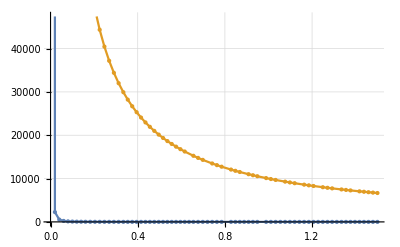

Will not graph individual modes since n^2 curves is too many for n>10

```mathematica
(*Clear the kernel's memory of any previous variables/functions*)
Clear["Global'*"];

(*Define our functions*)
sigma[n_,k_,p_,q_] := n/(2*(Pi^2)*Sqrt[k]*(p^2+q^2));
f[s_,c_] := (Sqrt[2/Pi]*Exp[-c^2/(2*s^2)])/(s*Erf[c/(Sqrt[2]*s)]);

(*Set our system constants*)
(* For our actual model. We'll use lambda = 5 nm, L = 500 nm => n = 100 *)
n=100;
kappa = 30;

(*Construct the system of n^2 equations for each mode's force*)
sys={};
Block[{$IterationLimit=n^2+20},
For[p=1,p<=n,p++,
For[q=1,q≤n,q++,
	sys = Join[sys,{f[sigma[n,kappa,p,q],c]}]
]
]
];
Print["System constructed"]
(*Print[sys]*)

(*Get an equation for the summed force*)
Print["Computing eq for total F"] 
totalF = Total[sys];

(*Graph the results*)
cMax = 1.5;

Print["Plotting total F"]
Plot[{Total[sys],n^2/c},{c,0,cMax},GridLines->Automatic, 
Mesh-> All, PlotPoints-> 10,MaxRecursion->3] (*Plot the summed force vs the appx for c<<1*)

If[n≤10,
Print["Plotting each mode's F"]
AbsoluteTiming[Plot[sys,{c,0,cMax},PlotRange->{{0,cMax},{0,200}},GridLines->Automatic, Mesh-> All,PlotPoints-> 10,MaxRecursion->3]],
Print["Will not graph individual modes since n^2 curves is too many for n>10"]
]
```

It seems like what we’re getting is much too small...